```mathematica
LaplaceTransform[Exp[-t]*HeavisideTheta[t],t,s]
```

1/(1+s)

```mathematica
LaplaceTransform[Exp[-2t]*HeavisideTheta[t],t,s]
```

1/(2+s)

```mathematica
Convolve[Exp[-t]*HeavisideTheta[t],Exp[-2t]*HeavisideTheta[t],t,x]
```

ⅇ^(-2 x) (-1+ⅇ^x) HeavisideTheta[x]

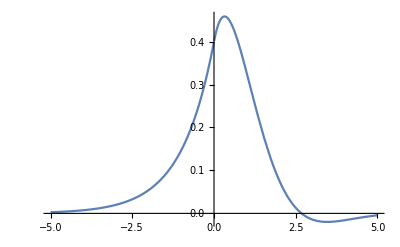

```mathematica
Plot[2/5*HeavisideTheta[t]*(Exp[-t]*Cos[t]+2*Exp[-t]*Sin[t])+2/5*Exp[t]*HeavisideTheta[-t],{t,-5,5}]
```